```mathematica
y[t_]:= (2*Exp[3*t ]+ Exp[3])/(Exp[(3*t)/2] * (2+ Exp[3]));
u[t_]:= (2*  (Exp[3*t] - Exp[3]) )/(Exp[(3*t)/2] * (2+ Exp[3]));
lambda[t_]:=  -u[t];
```

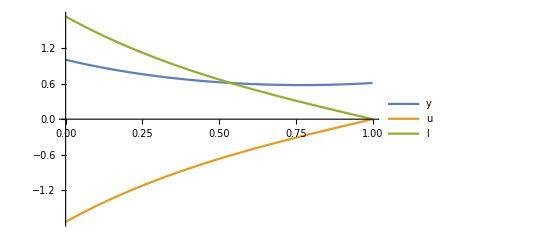

```mathematica
Plot[{y[t], u[t], lambda[t]}, {t,0,1}, PlotLegends->{"y", "u", "l"}]
```

```mathematica
g = y[t]^2 + 1/2 *  u[t]^2;
f = 1/2  *  y[t] + u[t];
```

```mathematica
D[y[t], {t,1}]- f//Simplify
D[lambda[t], {t,1}]  + 1/2* lambda[t] + 2* y[t]//Simplify
lambda[t] + u[t]//Simplify
```

0

0

0

```mathematica
Clear[u,sol]
u[x,t]= Sin[π x]* Sin[π t/2]
eq=D[T[x,t],t]-D[T[x,t],{x,2}]==u[x,t];
ic=T[x,0]==0*Sin[π x]+ 0*Sin[2π x];
bc={T[0,t]==0,T[1,t]==0};
bc={T[0,t]==0,T[1,t]==0};
(*bc={Derivative[1,0][T][0,t]==0,Derivative[1,0][T][1,t]==0};*)
(*Sin[π x]*Sin[2 π*t]*)
sol=DSolveValue[{eq,ic,bc},T[x,t],{x,t}];
Plot3D[sol,{t,0,1},{x,0,1},AxesLabel->{t,x,T}]
```

Sin[(π t)/2] Sin[π x]

-Graphics3D-

```mathematica
Plot3D[Sin[π x]* Sin[π t/2],{t,0,1},{x,0,1},AxesLabel->{t,x,T}]
```

-Graphics3D-

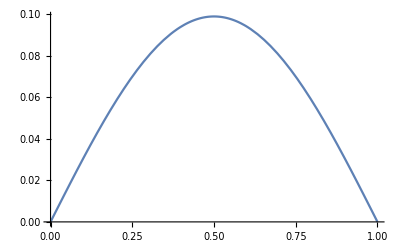

```mathematica
Plot[sol/.t-> 1, {x,0,1}]//FullSimplify
```

```mathematica
CForm[sol//Simplify]
```

(2*(Power(E,-(Power(Pi,2)*t)) - Cos((Pi*t)/2.) + 2*Pi*Sin((Pi*t)/2.))*Sin(Pi*x))/(Pi + 4*Power(Pi,3))

```mathematica
<<ToMatlab`
```

```mathematica
Manipulate[Plot[sol/.t->tee, {x,0,1}],  {tee,0,1}]
```